```mathematica
Clear["Global`*"]
```

```mathematica
Dynamic[BarChart[{Cycle/NumberOfCycles,OP/NM,1},BarOrigin->Left]]
Dynamic[Show[G3]]
Dynamic[Show[G4]]
Dynamic[Show[GS]]
Dynamic[Show[G5]]
Dynamic[ListLinePlot[Flatten@EnergyCriteria/2]]
Dynamic[ListLinePlot[Flatten@δe/2]]
Dynamic[Show[G3VD]]
Dynamic[Show[G4VD]]
```

```mathematica
Ung=200*10^9;
ν=0.3;
DD={{λ+2*μ,λ,0},{λ,λ+2μ,0},{0,0,μ}};
λ=ν*Ung/(1+ν)/(1-2*ν);
μ=Ung/2/(1+ν);
ρ=7850;
MatrixForm@DD;
ϵ0={{α*dt},{α*dt},{0}};
α=13*10^-15;
dt=10;
ROpt=0.05;(*Плотность*)
a=0.5;
a1=2;
a2=4;
ζ=N[24a/100];
Reg1=Parallelogram[{a2*a,2*a},{{0,a1*a},{a2*a,0}}];
Reg2=Parallelogram[{a2*a,2*a},{{0,a1*a},{-a2*a,0}}];
Reg3=Parallelogram[{a2*a,2*a},{{0,-a1*a},{a2*a,0}}];
Reg4=Parallelogram[{a2*a,2*a},{{0,-a1*a},{-a2*a,0}}];
(*Reg5=Disk[{3a,2a},a/2];*)
Reg1234=RegionUnion[Reg1,Reg2,Reg3,Reg4];
(*ℛ=RegionDifference[Reg1234,Reg5];*)
Reg=DiscretizeRegion[Reg1234,MeshCellLabel->{0->"Index"},MaxCellMeasure->0.02]
Coord=MeshCoordinates[Reg];
Polys=MeshCells[Reg,2];
```

-Graphics-

```mathematica
Coord[[11]]
```

{4.,2.}

```mathematica
NM=5;
NumberOfCycles=5;
δe=Table[0,{i,1,NumberOfCycles},{j,1,NM}];
EnergyCriteria=Table[0,{i,1,NumberOfCycles},{j,1,NM}];
For[i=1,i≤Length[Polys],i++,rho[i]=ROpt];
KoeffCriticalRadius=2;
num=3;
inc=1;
```

```mathematica
For[Cycle=1,Cycle≤NumberOfCycles,Cycle++,
For[OP=1,OP≤NM,OP++,
Width=Table[rho[i],{i,1,Length[Polys]}];
(*=====================================================================================================================================================*)(*Площадь i элемента*)
(*=====================================================================================================================================================*)S[i_]:=0.5*((Coord[[Polys[[i,1,1]],1]]-Coord[[Polys[[i,1,3]],1]])*(Coord[[Polys[[i,1,2]],2]]-Coord[[Polys[[i,1,3]],2]])-(Coord[[Polys[[i,1,2]],1]]-Coord[[Polys[[i,1,3]],1]])*(Coord[[Polys[[i,1,1]],2]]-Coord[[Polys[[i,1,3]],2]]));
(*=====================================================================================================================================================*)(*Коэффициенты функций формы i элемента*)
(*=====================================================================================================================================================*)(*i*)
ai[i_]:=Coord[[Polys[[i,1,2]],1]]*Coord[[Polys[[i,1,3]],2]]-Coord[[Polys[[i,1,3]],1]]*Coord[[Polys[[i,1,2]],2]];
bi[i_]:=Coord[[Polys[[i,1,2]],2]]-Coord[[Polys[[i,1,3]],2]];
ci[i_]:=Coord[[Polys[[i,1,3]],1]]-Coord[[Polys[[i,1,2]],1]];
(*j*)
aj[i_]:=Coord[[Polys[[i,1,3]],1]]*Coord[[Polys[[i,1,1]],2]]-Coord[[Polys[[i,1,1]],1]]*Coord[[Polys[[i,1,3]],2]];
bj[i_]:=Coord[[Polys[[i,1,3]],2]]-Coord[[Polys[[i,1,1]],2]];
cj[i_]:=Coord[[Polys[[i,1,1]],1]]-Coord[[Polys[[i,1,3]],1]];
(*m*)
am[i_]:=Coord[[Polys[[i,1,1]],1]]*Coord[[Polys[[i,1,2]],2]]-Coord[[Polys[[i,1,2]],1]]*Coord[[Polys[[i,1,1]],2]];
bm[i_]:=Coord[[Polys[[i,1,1]],2]]-Coord[[Polys[[i,1,2]],2]];
cm[i_]:=Coord[[Polys[[i,1,2]],1]]-Coord[[Polys[[i,1,1]],1]];
(*Функции формы*)
Ni[i_]:=1/(2S[i])*(ai[i]+bi[i]*x+ci[i]*y);
Nj[i_]:=1/(2S[i])*(aj[i]+bj[i]*x+cj[i]*y);
Nm[i_]:=1/(2S[i])*(am[i]+bm[i]*x+cm[i]*y);
(*Задание матрицы B*)
B[i_]:={
{D[Ni[i],x],0,D[Nj[i],x],0,D[Nm[i],x],0},
{0,D[Ni[i],y],0,D[D[Nj[i],y]],0,D[D[Nm[i],y]]},
{D[Ni[i],y],D[Ni[i],x],D[Nj[i],y],D[Nj[i],x],D[Nm[i],y],D[Nm[i],x]}
};
PreIntB[i_]:=Transpose[B[i]].DD.B[i];
Ke[i_]:=PreIntB[i]*S[i]*Width[[i]];
(*=====================================================================================================================================================*)(*Критерий Сильвестра и симметричность матрицы соблюдены*)
(*=====================================================================================================================================================*)StifnessMatrix=Table[0,{i,1,Length[Coord]*2},{j,1,Length[Coord]*2}];
For[b=1,b≤Length[Polys],b++,
NUM={Polys[[b,1,1]]*2-1,Polys[[b,1,1]]*2,Polys[[b,1,2]]*2-1,Polys[[b,1,2]]*2,Polys[[b,1,3]]*2-1,Polys[[b,1,3]]*2};
For[p=1,p<=6,p++,
For[g=1,g<=6,g++,
StifnessMatrix[[NUM[[p]],NUM[[g]]]]=Ke[b][[p,g]]+StifnessMatrix[[NUM[[p]],NUM[[g]]]];
];
];
];
(*=====================================================================================================================================================*)(*Формирование силовых факторов и перемещений*)
(*=====================================================================================================================================================*)Displacement=Table[δ[i],{i,1,Length[Coord]*2}];
Force=Table[f[i],{i,1,Length[Coord]*2}];
(*=====================================================================================================================================================*)(*Сосредоточенная нагрузка*)
(*=====================================================================================================================================================*)k1=46;Ang1=-90Degree;
(*k2=558;Ang2=80Degree;
k3=414;Ang3=85Degree;
k4=375;Ang4=120Degree;
k5=322;Ang5=75Degree;
k6=367;Ang6=80Degree;
k7=517;Ang7=-20Degree;
k8=579;Ang8=20Degree;
k9=2;Ang9=0Degree;*)
(*k10=310;Ang10=45Degree;
k11=421;Ang11=45Degree;
k12=258;Ang12=45Degree;
k13=322;Ang13=225Degree;*)
For[i=1,i≤Length[Coord]*2,i++,
f[i]=0;
];
f[k1*2-1]=1000000*2*Cos[Ang1];
(*f[k2*2-1]=129*2*Cos[Ang2];
f[k3*2-1]=284*2*Cos[Ang3];
f[k4*2-1]=205*2*Cos[Ang4];
f[k5*2-1]=91*2*Cos[Ang5];
f[k6*2-1]=130*2*Cos[Ang6];
f[k7*2-1]=35*2*Cos[Ang7];
f[k8*2-1]=104*2*Cos[Ang8];
f[k9*2-1]=250*Cos[Ang9];*)
(*f[k10*2-1]=100000*9.8*Cos[Ang10];
f[k11*2-1]=100000*9.8*Cos[Ang11];
f[k12*2-1]=100000*9.8*Cos[Ang12];
f[k13*2-1]=200000*9.8*Cos[Ang13];*)
f[k1*2]=1000000*Sin[Ang1];
(*f[k2*2]=129*Sin[Ang2];
f[k3*2]=284*Sin[Ang3];
f[k4*2]=205*Sin[Ang4];
f[k5*2]=91*Sin[Ang5];
f[k6*2]=130*Sin[Ang6];
f[k7*2]=35*Sin[Ang7];
f[k8*2]=104*Sin[Ang8];
f[k9*2]=259*Sin[Ang9];*)
(*f[k10*2]=100000*9.8*Sin[Ang10];
f[k11*2]=100000*9.8*Sin[Ang11];
f[k12*2]=100000*9.8*Sin[Ang12];
f[k13*2]=200000*9.8*Sin[Ang13];*)
(*=====================================================================================================================================================*)(*Массовые силы(Сила тяжести),Температурная нагрузка*)
(*=====================================================================================================================================================*)PreIntϵ[i_]:=Transpose[B[i]].DD.ϵ0;
For[b=1,b≤Length[Polys],b++,
NUM={Polys[[b,1,1]]*2-1,Polys[[b,1,1]]*2,Polys[[b,1,2]]*2-1,Polys[[b,1,2]]*2,Polys[[b,1,3]]*2-1,Polys[[b,1,3]]*2};
FMass=-S[b]*Width[[b]]*ρ*9.8*0;
TF=PreIntϵ[b]*10000000*0;
f[NUM[[1]]]=f[NUM[[1]]]+TF[[1]];
f[NUM[[2]]]=f[NUM[[2]]]+FMass/3+TF[[2]];
f[NUM[[3]]]=f[NUM[[3]]]+TF[[3]];
f[NUM[[4]]]=f[NUM[[4]]]+FMass/3+TF[[4]];
f[NUM[[5]]]=f[NUM[[5]]]+TF[[5]];
f[NUM[[6]]]=f[NUM[[6]]]+FMass/3+TF[[6]];
];
(*=====================================================================================================================================================*)(*Распределенные нагрузки*)
(*=====================================================================================================================================================*)N1=24;
N2=42;
Q=-500000*0;
L=2;
Incr=0;
For[b=1,b≤Length[Coord],b++,
If[Coord[[b,L]]==Coord[[N1,L]],Incr=Incr+1]
];
FPress=Q*Abs[(Coord[[N1,1]]-Coord[[N2,1]])]*Width[[1]];
(*=====================================================================================================================================================*)For[b=1,b≤Length[Coord],b++,
If[Coord[[b,L]]==Coord[[N1,L]],f[2*b-1]=f[2*b-1]+FPress/Incr]
];
(*=====================================================================================================================================================*)(*Формирование СЛАУ*)
(*=====================================================================================================================================================*)J=1;(*Номер компоненты*)
H=a2*a*2;(*Величина компоненты на границе*)
Equation={};
(*=====================================================================================================================================================*)For[i=1,i≤Length[Coord],i++,
If[Coord[[i,J]]==H,
δ[2*i-1]=0;
δ[2*i]=0
]];
(*d1=306;
d2=348;
d3=304;
d4=308;
d5=350;
d6=307;
d7=337;
d8=338;
d9=396; 
d10=95;
d11=343;
d12=298;
d13=341;
d14=299;
d15=342;
d16=404;
δ[2*d1-1]=0;
δ[2*d1]=0;
δ[2*d2-1]=0;
δ[2*d2]=0;
δ[2*d3-1]=0;
δ[2*d3]=0;
δ[2*d4-1]=0;
δ[2*d4]=0;
δ[2*d5-1]=0;
δ[2*d5]=0;
δ[2*d6-1]=0;
δ[2*d6]=0;
δ[2*d7-1]=0;
δ[2*d7]=0;
δ[2*d8-1]=0;
δ[2*d8]=0;
δ[2*d9-1]=0;
δ[2*d9]=0;
δ[2*d10-1]=0;
δ[2*d10]=0;
δ[2*d11-1]=0;
δ[2*d11]=0;
δ[2*d12-1]=0;
δ[2*d12]=0;
δ[2*d13-1]=0;
δ[2*d13]=0;
δ[2*d14-1]=0;
δ[2*d14]=0;
δ[2*d15-1]=0;
δ[2*d15]=0;
δ[2*d16-1]=0;
δ[2*d16]=0;*)
(*If[Coord[[i,J]]==0,
δ[2*i-1]=0;
δ[2*i]=0
];*)
(*=====================================================================================================================================================*)For[i=1,i≤Length[Coord],i++,
If[Not@NumberQ@δ[2*i-1]&&Not@NumberQ@δ[2*i](*Coord[[i,J]]≠H*)(*&&Coord[[i,J]]≠0,*),
Equation=Append[Equation,StifnessMatrix[[2i-1]].Displacement==f[2i-1]];
Equation=Append[Equation,StifnessMatrix[[2i]].Displacement==f[2i]];
];
];
Equation;
Length[Equation];
(*=====================================================================================================================================================*)DisplacementI={};
(*=====================================================================================================================================================*)For[i=1,i≤Length[Coord]*2,i++,
If[Not@NumberQ@δ[i],DisplacementI=Append[DisplacementI,δ[i]]];
];
Length@Table[NumberQ@δ[i],{i,1,Length[Coord]*2}];
Length[DisplacementI];
(*=====================================================================================================================================================*)
Sols=NSolve[Equation,DisplacementI];
DS=Displacement/.Sols[[1]];
CoordDeformed={};
CoordUndeformed={};
Sols;
(*=====================================================================================================================================================*)
For[i=1,i≤Length[Coord],i++,
CoordDeformed=Append[CoordDeformed,{Coord[[i,1]]+DS[[2i-1]],Coord[[i,2]]+DS[[2i]]}];
CoordUndeformed=Append[CoordUndeformed,{Coord[[i,1]],Coord[[i,2]]}];
];
δe[[Cycle,OP]]=DS[[2*k1]];
EnergyCriteria[[Cycle,OP]]=Sum[Transpose[ϝ[i]].Ke[i].ϝ[i],{i,1,Length[Polys]}];
(*=====================================================================================================================================================*)(*Обратный ход для получения напряжений*)
(*=====================================================================================================================================================*)For[b=1,b≤Length[Polys],b++,
NUM={Polys[[b,1,1]]*2-1,Polys[[b,1,1]]*2,Polys[[b,1,2]]*2-1,Polys[[b,1,2]]*2,Polys[[b,1,3]]*2-1,Polys[[b,1,3]]*2};
ϝ={{DS[[NUM[[1]]]]},{DS[[NUM[[2]]]]},{DS[[NUM[[3]]]]},{DS[[NUM[[4]]]]},{DS[[NUM[[5]]]]},{DS[[NUM[[6]]]]}};
ϵe[b]=B[b].ϝ;
σ[b]=DD.ϵe[b];
];
(*=====================================================================================================================================================*)Clear[CMP];
Clear[ϝ];
Clear[NUMF];
(*=====================================================================================================================================================*)(*Оптимизация формы*)
(*=====================================================================================================================================================*)Emin=2*10^3;
E0=Ung;
DP=3;
ñ=0.2;
m=ROpt*10^(-4);
RhoMin=ROpt*10^(-1);
(*=====================================================================================================================================================*)EE[i_]:=Emin+(rho[i]/ROpt)^DP*(E0-Emin);
NUMF[b_]:={Polys[[b,1,1]]*2-1,Polys[[b,1,1]]*2,Polys[[b,1,2]]*2-1,Polys[[b,1,2]]*2,Polys[[b,1,3]]*2-1,Polys[[b,1,3]]*2};
ϝ[b_]:={{DS[[NUMF[b][[1]]]]},{DS[[NUMF[b][[2]]]]},{DS[[NUMF[b][[3]]]]},{DS[[NUMF[b][[4]]]]},{DS[[NUMF[b][[5]]]]},{DS[[NUMF[b][[6]]]]}};
BB[i_]:=DP*rho[i]^(DP-1)*Transpose[ϝ[i]].Ke[i].ϝ[i];
DecreaseB=Table[BB[i][[1]],{i,1,Length[Polys]}]/Max[Table[BB[i][[1]],{i,1,Length[Polys]}]]*(3*OP)^(1/3);
(*=====================================================================================================================================================*)For[i=1,i≤Length[Polys],i++,
If[Max[rho[i]-m,RhoMin]>rho[i]*DecreaseB[[i,1]]^ñ,
rho[i]=Max[rho[i]-m,RhoMin],
];
If[Min[rho[i]+m,ROpt]<rho[i]*DecreaseB[[i,1]]^ñ,
rho[i]=Min[rho[i]+m,ROpt],
rho[i]=rho[i]*DecreaseB[[i,1]]^ñ
];
];
(*=====================================================================================================================================================*)(*Выравние массы всех элементов*)
(*=====================================================================================================================================================*)For[i=1,i<=Length[Polys],i++,If[rho[i]<RhoMin,rho[i]=RhoMin]];
For[i=1,i<=Length[Polys],i++,If[rho[i]<RhoMin,rho[i]=RhoMin]];
V1=Sum[rho[i]*S[i],{i,1,Length[Polys]}];
V2=Sum[S[i]*ROpt,{i,1,Length[Polys]}];
For[i=1,i≤Length[Polys],i++,rho[i]=rho[i]*V2/V1];
WD=Table[rho[i],{i,1,Length[Polys]}];
EqualS=Table[Sqrt[Sqrt[σ[i][[1,1]]^2+σ[i][[2,1]]^2]+3*σ[i][[3,1]]^2],{i,1,Length@Polys}];
(*=====================================================================================================================================================*)Graph3[OP,Cycle]=G3=Graphics[{Table[{EdgeForm[Black],Gray,Opacity[(WD[[i]]/Max[WD])],Polygon[{{CoordDeformed[[Polys[[i,1,1]]]][[1]],CoordDeformed[[Polys[[i,1,1]]]][[2]]},{CoordDeformed[[Polys[[i,1,2]]]][[1]],CoordDeformed[[Polys[[i,1,2]]]][[2]]},{CoordDeformed[[Polys[[i,1,3]]]][[1]],CoordDeformed[[Polys[[i,1,3]]]][[2]]}}]},{i,1,Length[Polys]}],Red,PointSize[Medium],Point[ForceCoordP],ForceCoordArrow}];
(*=====================================================================================================================================================*)Graph4[OP,Cycle]=G4=Graphics[Table[{EdgeForm[Black],Gray,Opacity[(WD[[i]]/Max[WD])],Polygon[{{CoordUndeformed[[Polys[[i,1,1]]]][[1]],CoordUndeformed[[Polys[[i,1,1]]]][[2]]},{CoordUndeformed[[Polys[[i,1,2]]]][[1]],CoordUndeformed[[Polys[[i,1,2]]]][[2]]},{CoordUndeformed[[Polys[[i,1,3]]]][[1]],CoordUndeformed[[Polys[[i,1,3]]]][[2]]}}]},{i,1,Length[Polys]}]];
(*=====================================================================================================================================================*)GraphStrain[OP,Cycle]=GS=
Graphics[Table[{EdgeForm[Black],Gray,Opacity[(EqualS[[i]]/Max[EqualS])^(1/5)],Polygon[{{CoordDeformed[[Polys[[i,1,1]]]][[1]],CoordDeformed[[Polys[[i,1,1]]]][[2]]},{CoordDeformed[[Polys[[i,1,2]]]][[1]],CoordDeformed[[Polys[[i,1,2]]]][[2]]},{CoordDeformed[[Polys[[i,1,3]]]][[1]],CoordDeformed[[Polys[[i,1,3]]]][[2]]}}]},{i,1,Length[Polys]}]];
Beep[];
];
Beep[];
(*=====================================================================================================================================================*)(*Вектор H, удаление проблемы шахматной доски.*)
(*=====================================================================================================================================================*)SquareS=Table[S[i],{i,1,Length@Polys}];
Rmin=Sqrt[Max@SquareS/Pi]*KoeffCriticalRadius;
XC[i_]:=(Coord[[Polys[[i,1,1]],1]]+Coord[[Polys[[i,1,2]],1]]+Coord[[Polys[[i,1,3]],1]])/3;
YC[i_]:=(Coord[[Polys[[i,1,1]],2]]+Coord[[Polys[[i,1,2]],2]]+Coord[[Polys[[i,1,3]],2]])/3;
ℋ[i_,j_]:=If[Rmin-Sqrt[(XC[i]-XC[j])^2+(YC[i]-YC[j])^2]>0,Rmin-Sqrt[(XC[i]-XC[j])^2+(YC[i]-YC[j])^2],0];
ℛ[i_]:=(1/Sum[ℋ[i,j],{j,1,Length[Polys]}])*Sum[ℋ[i,j]*rho[j]*DP*rho[j]^(DP-1)*Transpose[ϝ[j]].Ke[j].ϝ[j],{j,1,Length[Polys]}];
FilterMatrix=Parallelize[Table[ℛ[i][[1,1]],{i,1,Length[Polys]}]];
Beep[];
(*=====================================================================================================================================================*)V1R=Sum[FilterMatrix[[i]]*S[i],{i,1,Length[Polys]}];
FilterMatrixDensity=FilterMatrix*V2/V1R;
(*=====================================================================================================================================================*)Graph5[OP,Cycle]=G5=
Graphics[Table[{EdgeForm[Black],Gray,Opacity[(Abs@FilterMatrixDensity[[i]]/Max[FilterMatrixDensity])^(1/5)],Polygon[{{CoordUndeformed[[Polys[[i,1,1]]]][[1]],CoordUndeformed[[Polys[[i,1,1]]]][[2]]},{CoordUndeformed[[Polys[[i,1,2]]]][[1]],CoordUndeformed[[Polys[[i,1,2]]]][[2]]},{CoordUndeformed[[Polys[[i,1,3]]]][[1]],CoordUndeformed[[Polys[[i,1,3]]]][[2]]}}]},{i,1,Length[Polys]}]];
For[i=1,i≤Length@Polys,i++,
rho[i]=FilterMatrixDensity[[i]]
];
W=0.1;
Graph33D[OP,Cycle]=G3VD=
Graphics3D[
Table[{EdgeForm[Thickness[0]],GrayLevel[If[(Abs@FilterMatrixDensity[[i]]/Max[FilterMatrixDensity])^(1/5)>W,(Abs@FilterMatrixDensity[[i]]/Max[FilterMatrixDensity])^(1/5),0]],Opacity[If[(Abs@FilterMatrixDensity[[i]]/Max[FilterMatrixDensity])^(1/3)/2>W,1,0]],
Prism[{
{CoordUndeformed[[Polys[[i,1,1]]]][[1]],CoordUndeformed[[Polys[[i,1,1]]]][[2]],If[(Abs@FilterMatrixDensity[[i]]/Max[FilterMatrixDensity])^(1/5)/2>W,(Abs@FilterMatrixDensity[[i]]/Max[FilterMatrixDensity])^(1/num)/2*inc,0]},{CoordUndeformed[[Polys[[i,1,2]]]][[1]],CoordUndeformed[[Polys[[i,1,2]]]][[2]],If[(Abs@FilterMatrixDensity[[i]]/Max[FilterMatrixDensity])^(1/5)/2>W,(Abs@FilterMatrixDensity[[i]]/Max[FilterMatrixDensity])^(1/num)/2*inc,0]},{CoordUndeformed[[Polys[[i,1,3]]]][[1]],CoordUndeformed[[Polys[[i,1,3]]]][[2]],If[(Abs@FilterMatrixDensity[[i]]/Max[FilterMatrixDensity])^(1/5)/2>W,(Abs@FilterMatrixDensity[[i]]/Max[FilterMatrixDensity])^(1/num)/2*inc,0]},
{CoordUndeformed[[Polys[[i,1,1]]]][[1]],CoordUndeformed[[Polys[[i,1,1]]]][[2]],If[(Abs@FilterMatrixDensity[[i]]/Max[FilterMatrixDensity])^(1/5)/2>W,-(Abs@FilterMatrixDensity[[i]]/Max[FilterMatrixDensity])^(1/num)/2*inc,0]},{CoordUndeformed[[Polys[[i,1,2]]]][[1]],CoordUndeformed[[Polys[[i,1,2]]]][[2]],If[(Abs@FilterMatrixDensity[[i]]/Max[FilterMatrixDensity])^(1/5)/2>W,-(Abs@FilterMatrixDensity[[i]]/Max[FilterMatrixDensity])^(1/num)/2*inc,0]},{CoordUndeformed[[Polys[[i,1,3]]]][[1]],CoordUndeformed[[Polys[[i,1,3]]]][[2]],If[(Abs@FilterMatrixDensity[[i]]/Max[FilterMatrixDensity])^(1/5)/2>W,-(Abs@FilterMatrixDensity[[i]]/Max[FilterMatrixDensity])^(1/num)/2*inc,0]}
}]},
{i,1,Length[Polys]}]];
DF=0.1;
Graph43D[OP,Cycle]=G4VD=
Graphics3D[
Table[{EdgeForm[Thickness[0]],Gray,Opacity[If[(WD[[i]]/Max[WD])>DF,1,0]],
Prism[{
{CoordUndeformed[[Polys[[i,1,1]]]][[1]],CoordUndeformed[[Polys[[i,1,1]]]][[2]],If[(Abs@FilterMatrixDensity[[i]]/Max[FilterMatrixDensity])^(1/5)/2>DF,(WD[[i]]/Max[WD])/2,0]},{CoordUndeformed[[Polys[[i,1,2]]]][[1]],CoordUndeformed[[Polys[[i,1,2]]]][[2]],If[(Abs@FilterMatrixDensity[[i]]/Max[FilterMatrixDensity])^(1/5)/2>DF,(WD[[i]]/Max[WD])/2,0]},{CoordUndeformed[[Polys[[i,1,3]]]][[1]],CoordUndeformed[[Polys[[i,1,3]]]][[2]],If[(Abs@FilterMatrixDensity[[i]]/Max[FilterMatrixDensity])^(1/5)/2>DF,(WD[[i]]/Max[WD])/2,0]},
{CoordUndeformed[[Polys[[i,1,1]]]][[1]],CoordUndeformed[[Polys[[i,1,1]]]][[2]],If[(Abs@FilterMatrixDensity[[i]]/Max[FilterMatrixDensity])^(1/5)/2>DF,-(WD[[i]]/Max[WD])/2,0]},{CoordUndeformed[[Polys[[i,1,2]]]][[1]],CoordUndeformed[[Polys[[i,1,2]]]][[2]],If[(Abs@FilterMatrixDensity[[i]]/Max[FilterMatrixDensity])^(1/5)/2>DF,-(WD[[i]]/Max[WD])/2,0]},{CoordUndeformed[[Polys[[i,1,3]]]][[1]],CoordUndeformed[[Polys[[i,1,3]]]][[2]],If[(Abs@FilterMatrixDensity[[i]]/Max[FilterMatrixDensity])^(1/5)/2>DF,-(WD[[i]]/Max[WD])/2,0]}
}]},
{i,1,Length[Polys]}]
,ViewPoint->Default];
];
```

```mathematica
(FilterMatrixDensity[[2]]/Max@FilterMatrixDensity)^(1/5)
```

0.598952

# Результаты оптимизаций различных структур

```mathematica
(*Полученные результаты*)
-Graphics3D-
-Graphics3D-
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

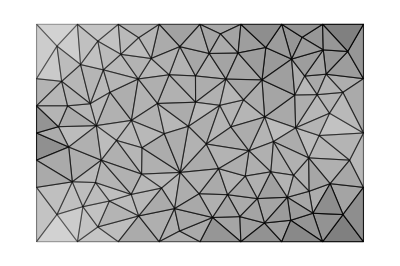

```mathematica
Graph4[1,1]
```

```mathematica
Export["E:\\TopologyOpt\\Gif12.avi",Animate[Show[Graph4[1,i]],{i,1,NumberOfCycles,1}]]
```

E:\TopologyOpt\Gif12.avi

```mathematica
Animate[Show[Graph4[1,i]],{i,1,NumberOfCycles,1}]
```

```mathematica
Export["E:\\TopologyOpt\\Gif51.avi",Animate[Show[Graph33D[NM+1,i]],{i,1,NumberOfCycles,1}]]
```

E:\TopologyOpt\Gif51.avi

```mathematica
Animate[Show[Graph3[1,i]],{i,1,NumberOfCycles,1}]
```

```mathematica
Export["E:\\TopologyOpt\\GraphDisplacement1.avi",Animate[ListLinePlot[δe[[i]],PlotLegends->{ToString[i]<>" Iteration"},PlotRange->{{1,10},{Min[δe],Max[δe]}}],{i,1,NumberOfCycles,1}]]
```

E:\TopologyOpt\GraphDisplacement1.avi

```mathematica
Animate[ListLinePlot[δe[[i]],PlotLegends->{ToString[i]<>" Iteration"},PlotRange->{{1,10},{Min[δe],Max[δe]}}],{i,1,NumberOfCycles,1}]
```

```mathematica
δe
```

δe

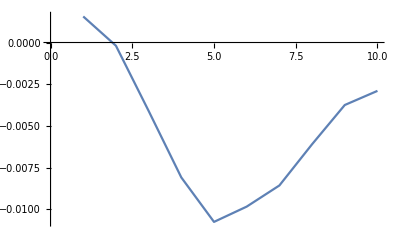

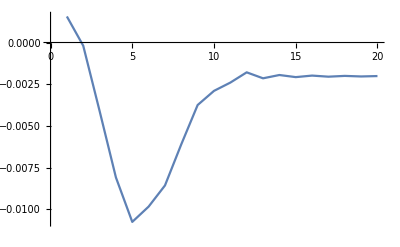

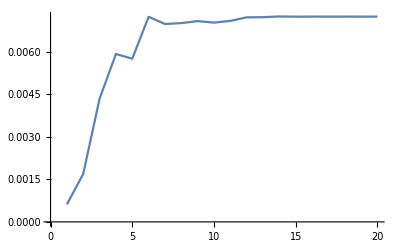

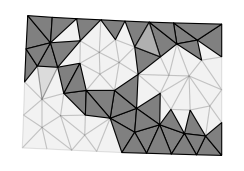

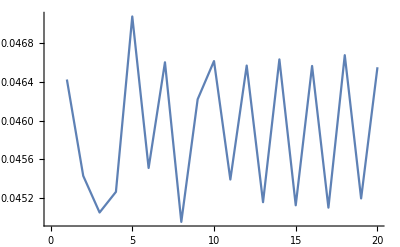

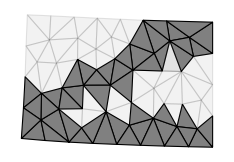

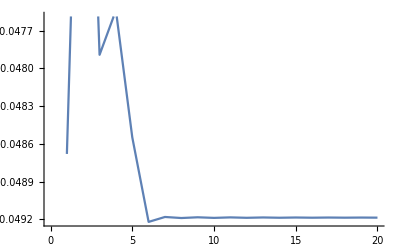

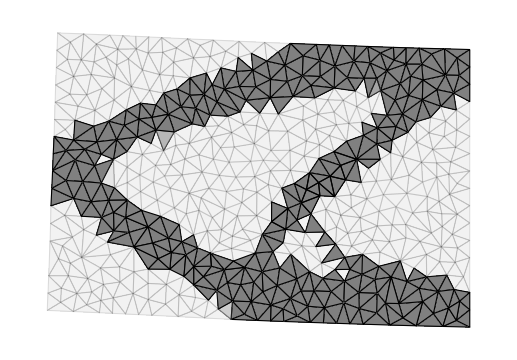

```mathematica
MatrixForm@δe
```

(0.170436 | 0.145446 | 0.133838 | 0.13183 | 0.132251 | 0.133779 | 0.135149 | 0.135782 | 0.13633 | 0.136772
0.129229 | 0.121599 | 0.133605 | 0.134694 | 0.135733 | 0.135888 | 0.135533 | 0.135768 | 0.135702 | 0.135709
0.154157 | 0.11455 | 0.131139 | 0.130244 | 0.130768 | 0.131026 | 0.131431 | 0.131649 | 0.131743 | 0.131847
0.156418 | 0.11364 | 0.129673 | 0.128425 | 0.129263 | 0.129765 | 0.130299 | 0.130676 | 0.13097 | 0.131181
0.150898 | 0.113237 | 0.12895 | 0.127643 | 0.128421 | 0.12889 | 0.129126 | 0.129451 | 0.129593 | 0.129748)

```mathematica
Sum[Transpose[ϝ[i]].Ke[i].ϝ[i],{i,1,Length[Polys]}]
```

{{132162.}}

```mathematica
EnergyCriteria
```

{{{{136635.}},{{142537.}},{{131161.}},{{129193.}},{{129606.}},{{131103.}},{{132446.}},{{133066.}},{{133603.}},{{134036.}}},{{{126645.}},{{119167.}},{{130933.}},{{132000.}},{{133018.}},{{133171.}},{{132823.}},{{133053.}},{{132988.}},{{132995.}}},{{{151074.}},{{112259.}},{{128516.}},{{127639.}},{{128153.}},{{128406.}},{{128802.}},{{129016.}},{{129108.}},{{129210.}}},{{{153290.}},{{111368.}},{{127080.}},{{125857.}},{{126678.}},{{127170.}},{{127693.}},{{128062.}},{{128351.}},{{128557.}}},{{{147880.}},{{110972.}},{{126371.}},{{125090.}},{{125853.}},{{126312.}},{{126543.}},{{126862.}},{{127001.}},{{127153.}}}}

```mathematica
Flatten@EnergyCriteria
```

{136635.,142537.,131161.,129193.,129606.,131103.,132446.,133066.,133603.,134036.,126645.,119167.,130933.,132000.,133018.,133171.,132823.,133053.,132988.,132995.,151074.,112259.,128516.,127639.,128153.,128406.,128802.,129016.,129108.,129210.,153290.,111368.,127080.,125857.,126678.,127170.,127693.,128062.,128351.,128557.,147880.,110972.,126371.,125090.,125853.,126312.,126543.,126862.,127001.,127153.}

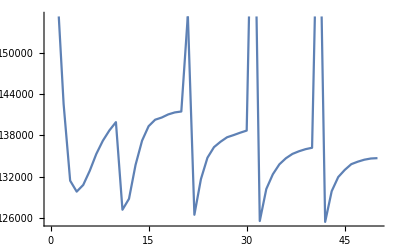

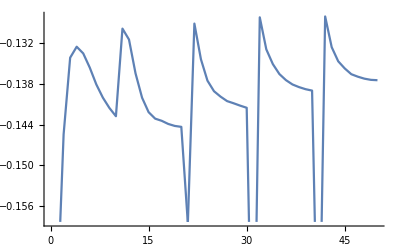

```mathematica
ListLinePlot[Flatten@EnergyCriteria]
ListLinePlot[Flatten@δe]
```

```mathematica
Flatten@EnergyCriteria[[2]]
```

{127231.,128819.,133720.,137239.,139333.,140269.,140583.,141038.,141325.,141460.}

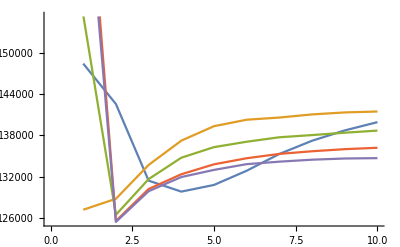

```mathematica
ListLinePlot[{Flatten@EnergyCriteria[[1]],Flatten@EnergyCriteria[[2]],Flatten@EnergyCriteria[[3]],Flatten@EnergyCriteria[[4]],Flatten@EnergyCriteria[[5]]}]
```

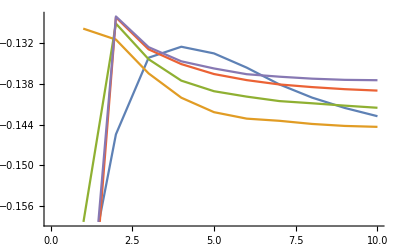

```mathematica
ListLinePlot[{Flatten@δe[[1]],Flatten@δe[[2]],Flatten@δe[[3]],Flatten@δe[[4]],Flatten@δe[[5]]}]
```

```mathematica
δe
```

{{0.170436,0.145446,0.133838,0.13183,0.132251,0.133779,0.135149,0.135782,0.13633,0.136772},{0.129229,0.121599,0.133605,0.134694,0.135733,0.135888,0.135533,0.135768,0.135702,0.135709},{0.154157,0.11455,0.131139,0.130244,0.130768,0.131026,0.131431,0.131649,0.131743,0.131847},{0.156418,0.11364,0.129673,0.128425,0.129263,0.129765,0.130299,0.130676,0.13097,0.131181},{0.150898,0.113237,0.12895,0.127643,0.128421,0.12889,0.129126,0.129451,0.129593,0.129748}}

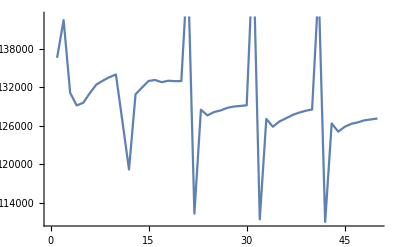

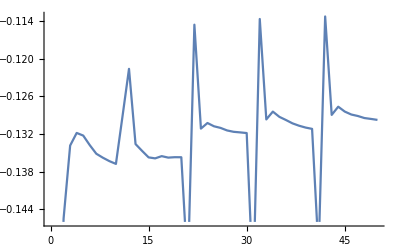

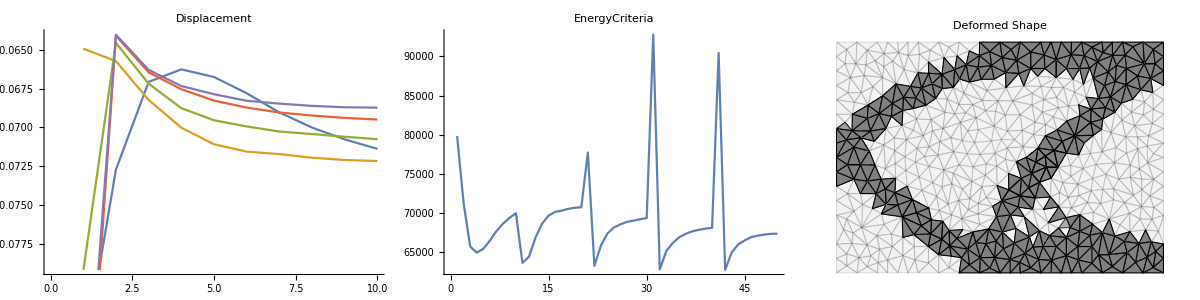

```mathematica
K1=Grid[{{
ListLinePlot[δe/2,ImageSize->Medium,PlotLabel->"Displacement"],
ListLinePlot[Flatten@EnergyCriteria/2,PlotRange->All,ImageSize->Medium,PlotLabel->"EnergyCriteria"],Show[G4,ImageSize->Medium,PlotLabel->"Deformed Shape"]}},Frame->True]
```

```mathematica
Export["E:\\TopologyOpt\\Displacement.txt",Flatten@δe/2]
Export["E:\\TopologyOpt\\DisplacementI.png",K1]
```

E:\TopologyOpt\Displacement.txt

E:\TopologyOpt\DisplacementI.png